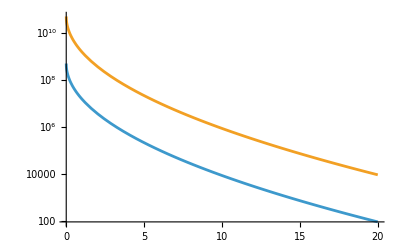

```mathematica
mu0 = 0;
sigmaE = Sqrt[6.];
barz0 = Exp[-mu0 + sigmaE^2/2];
barz[x_]:=barz0*Exp[sigmaE*Sqrt[2*x]]

LogPlot[{10^10/barz[x], 10^12/barz[x]}, {x, 0, 20}]
```